#### Input, output and display

An undirected edge between u and v, with character <-> can be entered as [esc] ue [esc]
An directed edge between u and v, with character -> can be entered as [esc] de [esc], or you can just use ->



```mathematica
Graph[{1<->2, 3<->2}]
```

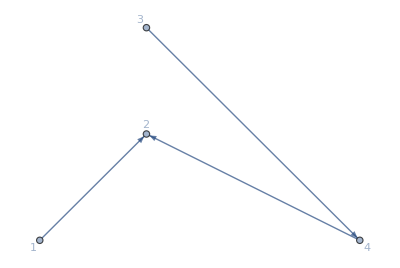

```mathematica
g=Graph[{1->2, 3->4,4->2},VertexLabels->All,GraphLayout->"PlanarEmbedding"]
```

#### Neighbors

Paths, Cycles, and Flows

#### Topological sort

Topological Sort can turn a Directed Acyclic Graph (DAG) into array

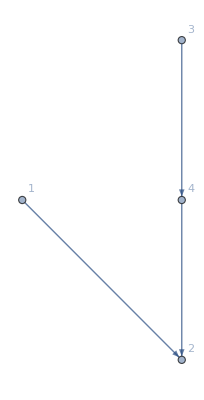

```mathematica
g=Graph[{1->2, 3->4,4->2},VertexLabels->All]
```

```mathematica
TopologicalSort[g]
```

{3,4,1,2}

#### Shortest path

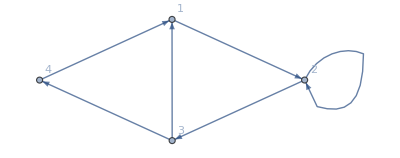

```mathematica
g=Graph[{1->2,2->3,3->4,4->1,3->1,2->2},VertexLabels->All]
```

```mathematica
FindShortestPath[g,1,3]
```

{1,2,3}

Graph distance can use three methods with O(n log n) : Dijkstra , BellmanFord and UnitWeight

```mathematica
GraphDistance[g,1,3]
```

2

Graph distance matrix takes O(n^3)

```mathematica
GraphDistanceMatrix[g]//MatrixForm
```

(0 | 1 | 2 | 3
2 | 0 | 1 | 2
1 | 2 | 0 | 1
1 | 2 | 3 | 0)

#### Hamiltonian Path

```mathematica
FindHamiltonianPath[g]
```

{1,2,3,4}

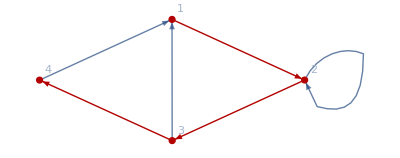

```mathematica
HighlightGraph[g,PathGraph[FindHamiltonianPath[g],DirectedEdges->True]]
```